```mathematica
ClearAll["Global`*"];
MM=1;aa=0.5;En=0.98;Lz=3.3;eps=-0.001;
r0=40.323;th0=N[Pi/2];
Print["params {MM,aa,En,Lz,eps} = ",InputForm@{MM,aa,En,Lz,eps}];
```

```mathematica
Get["/home/nealb/Projects/Kerr Geodesics-old-python/GRQUICK.m"];

QQ=0;
DeltaG=r^2-2 MM r+aa^2+QQ^2;
SigmaG=r^2+aa^2 Cos[th]^2;
g[0,0]=-(DeltaG-aa^2 Sin[th]^2)/SigmaG;
g[1,1]=SigmaG/DeltaG;
g[2,2]=SigmaG;
g[3,3]=((r^2+aa^2)^2-DeltaG aa^2 Sin[th]^2) Sin[th]^2/SigmaG;
g[0,3]=-aa Sin[th]^2 (2 MM r-QQ^2)/SigmaG;
g[3,0]=g[0,3];

G[1,1]=1/g[1,1];
G[2,2]=1/g[2,2];
G[0,0]=g[3,3]/(g[0,0] g[3,3]-g[0,3]^2);
G[3,3]=g[0,0]/(g[0,0] g[3,3]-g[0,3]^2);
G[0,3]=G[3,0]=-g[0,3]/(g[0,0] g[3,3]-g[0,3]^2);
G[0,1]=G[0,2]=G[1,0]=G[1,2]=G[1,3]=G[2,0]=G[2,1]=G[2,3]=G[3,1]=G[3,2]=0;

Metin[{{g[0,0],0,0,g[0,3]},{0,g[1,1],0,0},{0,0,g[2,2],0},{g[3,0],0,0,g[3,3]}},{t,r,th,ph}]

Clear[ϵ];
PD[1]=g[1,1] PU1;
PD[2]=g[2,2] PU2;
HamG=(1/2) Simplify[Sum[Sum[G[i,j] PD[i] PD[j],{i,0,3}],{j,0,3}]];
XX=HamG/. {PD[0]->-En-(ϵ/2)(g[0,3]+2 aa g[0,0]),PD[3]->Lz-(ϵ/2)(g[3,3]+2 aa g[0,3])};
XX2sym=ϵ^2 Simplify[Coefficient[XX,ϵ,2]];
XX2=XX2sym/. ϵ->eps;
Print["XX2 vs our H2X: ",InputForm@Simplify[XX2-H2X]];
```

```mathematica
(* ===================================================================POTENTIALS-- CORRECTED 2026-09-14 Built from XX2,the O(eps^2) part of the full Hamiltonian,derived in the GRQUICK cell above rather than transcribed.Verified there:Simplify[XX2-H2X]=0 to floating-point residue,so the old H2X was always right.The error was in how H2 was assembled into V2.The old V2X applied the overall 1/Sin[th]^2 to the H2 term and carried Cos[th] where Cos[th]^2 belongs.V1X was always correct.Effect: ~1.4e-4 at the polar turning points,exactly zero at the equator-- so every verification constant in use passed while V2 was wrong.The off-equator V2 check below is the one that catches it.Run AFTER the GRQUICK cell (needs XX2) and after the parameter cell (needs MM,aa,En,Lz,eps,r0,th0).
===================================================================*)ClearAll[V1X,V2X,V1f,V2f,dV1dr,dV1dth,dV2dr,dV2dth,DeltaF,mk];

DeltaX=r^2-2 MM r+aa^2;
SigmaX=r^2+aa^2 Cos[th]^2;

V1X=(En (r^2+aa^2)-aa Lz)^2+DeltaX r^2 eps (Lz-2 aa En)-DeltaX (kk+r^2)-2 r^2 DeltaX XX2;

V2X=kk-aa^2 Cos[th]^2-(aa^2 Sin[th]^2 En^2-2 aa En Lz+Lz^2/Sin[th]^2)+aa^2 Cos[th]^2 eps (Lz-2 aa En)-2 aa^2 Cos[th]^2 XX2;

mk[e_]:=Function[{rv,tv,kv},Evaluate[e/. {r->rv,th->tv,kk->kv}]];
V1f=mk[V1X];V2f=mk[V2X];
dV1dr=mk[D[V1X,r]];dV1dth=mk[D[V1X,th]];
dV2dr=mk[D[V2X,r]];dV2dth=mk[D[V2X,th]];
DeltaF=Function[{rv},Evaluate[DeltaX/. r->rv]];

(*----exact identities----*)
Print["dV1/dkappa + Delta (must be 0): ",InputForm@Chop@Simplify[D[V1X,kk]+DeltaX]];
Print["dV2/dkappa - 1 (must be 0): ",InputForm@Chop@Simplify[D[V2X,kk]-1]];

(*----verification constants----*)
Print["--- V1 ---"];
Print["V1f[40.323, 1.4,  K0] = ",InputForm@V1f[40.323,1.4,9.5110420912],"    want 32.1574143176"];
Print["V1f[40.323, Pi/2, K0] = ",InputForm@V1f[40.323,th0,9.5110420912],"    want 2.643695021"];
Print["Sqrt[V1]/r0^2 = ",InputForm@(Sqrt[V1f[r0,th0,9.5110420912]]/r0^2),"    want 1.0000000114e-3   (his PRi)"];
Print["--- V2 ---"];
Print["V2f[40.323, Pi/2, K0] = ",InputForm@V2f[40.323,th0,9.5110420912],"    want 1.614942091"];
Print["V2f[40.323, 1.4,  K0] = ",InputForm@V2f[40.323,1.4,9.5110420912],"    want 1.2894479245955830   <-- THE NEW CHECK"];
Print["      (the old, wrong V2 gave 1.2907118715486003 and passed"];
Print["       every other constant in the list)"];
Print["Sqrt[V2]/r0^2 = ",InputForm@(Sqrt[V2f[r0,th0,9.5110420912]]/r0^2),"    want 0.000781578862   (his PU2i)"];
Print["--- Delta ---"];
Print["DeltaF[r0] = ",InputForm@DeltaF[r0],"    want 1545.548329"];
```

```mathematica
ThetaTT=aa^2 Sin[th]^2;
ThetaTP=aa;
ThetaPP=1/Sin[th]^2;
H2Xprof=eps^2/(8 SigmaX) (-4 aa^2 DeltaX+(5 aa^4+r^4+2 aa^2 r^2-8 MM aa^2 r) Sin[th]^2-aa^2 DeltaX Sin[th]^4);
V2Xprof=kk-aa^2 Cos[th]^2-(ThetaTT En^2-2 ThetaTP En Lz+ThetaPP Lz^2)+aa^2 Cos[th]^2 eps (Lz-2 aa En)-2 aa^2 Cos[th]^2 H2Xprof;
V2fp=mk[V2Xprof];
Print["V2fp[40.323, 1.4, K0] = ",InputForm@V2fp[40.323,1.4,9.5110420912]];
Print["V2X - V2Xprof = ",InputForm@Chop@Simplify[V2X-V2Xprof]];
```

```mathematica
Print["V2fp now: ",InputForm@V2fp[40.323,1.4,9.5110420912]];
Print["diff: ",InputForm@Chop@Simplify[V2X-V2Xprof]];
```

```mathematica
SetDirectory[NotebookDirectory[]];
carter=Import["../data/DATA_CARTER.dat","Table"];
Print["rows: ",Length[carter],"   lam: ",carter[[1,1]]," to ",carter[[-1,1]]];

carterLamMax=1000;   (*NOT lamMax-that name is the integration horizon*)
carterSub=Select[carter,#[[1]]<=carterLamMax&][[;;;;10]];
Kfun=Interpolation[carterSub,InterpolationOrder->8];
Kdot=Kfun';

Print["{Kfun[0], Kdot[0]} = ",InputForm@{Kfun[0],Kdot[0]}];
(*If Interpolation fails,Kfun' returns Kfun itself and Kdot gives~9.5 where slopes~1e-4 belong;everything downstream then blows up.*)
Print["Kdot off-node (want O(1e-4..1e-1), NOT O(9.5)): ",InputForm@Kdot[7.3117]];
```

```mathematica
k0=Kfun[0];
Print["k0 = ",InputForm@k0,"   (expect 9.5110420912)"];
Print["{V1f, V2f} = ",InputForm@{V1f[r0,th0,k0],V2f[r0,th0,k0]}];
Print["Sqrt[V1]/r0^2 = ",InputForm@(Sqrt[V1f[r0,th0,k0]]/r0^2)];
Print["Delta(r0) = ",InputForm@DeltaF[r0]];

(*Expect V1=2.643695021,V2=1.614942091,Sqrt[V1]/r0^2=1.0000000114e-3)
```

```mathematica
refR=Import["../data/reference_r.dat","Table"];
refTh=Import["../data/reference_th.dat","Table"];
refRInt=Interpolation[refR,InterpolationOrder->5];
refThInt=Interpolation[refTh,InterpolationOrder->5];
Print["ref lam ranges: r ",refR[[{1,-1},1]],"   th ",refTh[[{1,-1},1]]];
```

```mathematica
(* ===================================================================SIGNED-MOMENTUM SOLVER-- replaces the segmented integrator Integrates (r,th,Pr,Pth) with Pr,Pth as SIGNED state variables:r'=Pr 2 Pr Pr'=dV1/dlam th'=Pth 2 Pth Pth'=dV2/dlam The constraint is handed to NDSolve undifferentiated.No square roots,no sign flags,no events,no restarts,no nudges-- Pr and Pth pass through zero on their own,so a turning point is an ordinary point of the flow.The segmented scheme existed to work around dividing by a velocity that vanishes twice per radial period.Writing r'=Pr instead of r'=sr Sqrt[u1] removes that division at the source.Measured on the corrected potentials,lam 0 to 1000:segmented max|dr| =1.48~80 s,1875 segments this max|dr| =1.8e-4~31 s,one NDSolve call Writes into traj/trajC in the old column layout {lam,r,th,u1,u2,srC,stC} with u1=Pr^2,u2=Pth^2 and the sign columns carrying Sign[Pr],Sign[Pth],so trajC,rInt,thInt,the crossing cell,islandAreas and the dR comparison all work unchanged.Needs the corrected V1X/V2X,Kfun,r0,th0,refRInt,refThInt.
===================================================================*)ClearAll[rS,thS,PrS,PthS,lamS];

fsOrder=8;
fsStep=0.01;
fsLamMax=1000;
dLamOut=0.01;

VrS=V1X/. {r->rS[lamS],th->thS[lamS],kk->Kfun[lamS]};
VthS=V2X/. {r->rS[lamS],th->thS[lamS],kk->Kfun[lamS]};

EqR=2 D[rS[lamS],lamS] D[D[rS[lamS],lamS],lamS]-D[VrS,lamS]/.
{Derivative[1][rS][lamS]->PrS[lamS],Derivative[2][rS][lamS]->D[PrS[lamS],lamS],Derivative[1][thS][lamS]->PthS[lamS],Derivative[2][thS][lamS]->D[PthS[lamS],lamS]};
EqTh=2 D[thS[lamS],lamS] D[D[thS[lamS],lamS],lamS]-D[VthS,lamS]/.
{Derivative[1][rS][lamS]->PrS[lamS],Derivative[2][rS][lamS]->D[PrS[lamS],lamS],Derivative[1][thS][lamS]->PthS[lamS],Derivative[2][thS][lamS]->D[PthS[lamS],lamS]};

PrI=Sqrt[V1f[r0,th0,Kfun[0]]];
PthI=Sqrt[V2f[r0,th0,Kfun[0]]];

Print["order ",fsOrder,", step ",fsStep,", to lam ",fsLamMax];
Print["Pr[0]  = ",InputForm@PrI,"   Pr[0]/r0^2 = ",InputForm@(PrI/r0^2),"   (his PRi = 0.001)"];
Print["Pth[0] = ",InputForm@PthI,"   Pth[0]/r0^2 = ",InputForm@(PthI/r0^2),"   (his PU2i = 0.000781579)"];
Print["Kfun domain ",InputForm@First[Kfun["Domain"]]];

timing=AbsoluteTiming[solS=Quiet@NDSolve[{D[rS[lamS],lamS]==PrS[lamS],D[thS[lamS],lamS]==PthS[lamS],EqR==0,EqTh==0,rS[0]==r0,thS[0]==th0,PrS[0]==PrI,PthS[0]==PthI},{rS,thS,PrS,PthS},{lamS,0,fsLamMax},Method->{"FixedStep",Method->{"ExplicitRungeKutta","DifferenceOrder"->fsOrder}},StartingStepSize->fsStep,MaxSteps->10^8]][[1]];

If[Head[solS]=!=List||solS==={},Print["NDSolve FAILED"],Module[{rf,tf,pf,qf,lamHi,res1,res2},{rf,tf,pf,qf}={rS,thS,PrS,PthS}/. solS[[1]];
lamHi=rf[[1,1,2]];
Print["reached lam = ",InputForm@lamHi,"   time ",timing," s"];
traj=Table[{lm,rf[lm],tf[lm],pf[lm]^2,qf[lm]^2,Sign[pf[lm]],Sign[qf[lm]]},{lm,0.,lamHi-dLamOut,dLamOut}];
trajC=traj;
rInt=Interpolation[Transpose[{traj[[All,1]],traj[[All,2]]}],InterpolationOrder->1];
thInt=Interpolation[Transpose[{traj[[All,1]],traj[[All,3]]}],InterpolationOrder->1];
Print["traj rows: ",Length[traj]];
Print["r range:  ",InputForm@MinMax[traj[[All,2]]]];
Print["th range: ",InputForm@MinMax[traj[[All,3]]]];
res1=Table[Abs[pf[lm]^2-V1f[rf[lm],tf[lm],Kfun[lm]]],{lm,0.,lamHi-0.1,0.25}];
res2=Table[Abs[qf[lm]^2-V2f[rf[lm],tf[lm],Kfun[lm]]],{lm,0.,lamHi-0.1,0.25}];
Print["|Pr^2 - V1|  median ",InputForm@Median[res1],"   max ",InputForm@Max[res1]];
Print["|Pth^2 - V2| median ",InputForm@Median[res2],"   max ",InputForm@Max[res2]];
Print["=== max |dr| and |dth| in 50-lam windows ==="];
Print[TableForm[Table[{w,w+50,Max[Table[Abs[rInt[lm]-refRInt[lm]],{lm,w,Min[w+50,lamHi-0.1],0.05}]],Max[Table[Abs[thInt[lm]-refThInt[lm]],{lm,w,Min[w+50,lamHi-0.1],0.05}]]},{w,0.,Min[950.,lamHi-51.],50.}],TableHeadings->{None,{"from","to","max |dr|","max |dth|"}}]];]
]
```

```mathematica
Module[{rf,tf,pf,qf,grid,prs,zeros,tab,nOf},{rf,tf,pf,qf}={rS,thS,PrS,PthS}/. solS[[1]];
nOf[lm_]:=dV1dr[rf[lm],tf[lm],Kfun[lm]] pf[lm]+dV1dth[rf[lm],tf[lm],Kfun[lm]] qf[lm]-DeltaF[rf[lm]] Kdot[lm];
grid=Range[0.,990.,0.01];
prs=pf/@grid;
zeros=Flatten@Position[Most[Sign[prs]] Rest[Sign[prs]],-1];
tab=Table[Module[{a=grid[[i]],b=grid[[i+1]],lP,lN},lP=x/. FindRoot[pf[x],{x,a,b}];
lN=Quiet@Check[x/. FindRoot[nOf[x],{x,a,b}],Missing[]];
{a,lP,lN,If[NumericQ[lN],lN-lP,Missing[]]}],{i,Take[zeros,UpTo[25]]}];
Print[TableForm[tab,TableHeadings->{None,{"grid lam","zero of Pr","zero of N","gap"}}]];
Print["gap/h, worst: ",InputForm@(Max[Abs[Select[tab[[All,4]],NumericQ]]]/0.01)]]
```

```mathematica
(*Residuals of u1 and u2 against V1 and V2*)
trajC=DeleteDuplicatesBy[traj,First];
lamA=trajC[[All,1]];rA=trajC[[All,2]];thA=trajC[[All,3]];
u1A=trajC[[All,4]];u2A=trajC[[All,5]];
srA=trajC[[All,6]];stA=trajC[[All,7]];
vrA=srA Sqrt[Clip[u1A,{0.,Infinity}]];
vthA=stA Sqrt[Clip[u2A,{0.,Infinity}]];

rInt=Interpolation[Transpose[{lamA,rA}],InterpolationOrder->1];
thInt=Interpolation[Transpose[{lamA,thA}],InterpolationOrder->1];

res1=Table[{lamA[[i]],Abs[u1A[[i]]-V1f[rA[[i]],thA[[i]],Kfun[lamA[[i]]]]]+10^-18},{i,Length[lamA]}];
res2=Table[{lamA[[i]],Abs[u2A[[i]]-V2f[rA[[i]],thA[[i]],Kfun[lamA[[i]]]]]+10^-18},{i,Length[lamA]}];

Print["points: ",Length[trajC],"   lam range: ",MinMax[lamA]];
Print["r start/mid/end: ",InputForm@{rA[[1]],rA[[Floor[Length[rA]/2]]],rA[[-1]]}];
Print["median |u1-V1|: ",Median[res1[[All,2]]],"   max: ",Max[res1[[All,2]]]];
Print["median |u2-V2|: ",Median[res2[[All,2]]],"   max: ",Max[res2[[All,2]]]];
(*Expect medians~5e-8 and~2e-10,flat,no secular growth.*)

Rasterize[ListLogPlot[{res1[[;;;;10]],res2[[;;;;10]]},Joined->True,PlotRange->All,Frame->True,Axes->False,ImageSize->300,PlotLegends->{"|u1-V1|","|u2-V2|"},FrameLabel->{"lambda","constraint residual"}],ImageResolution->150]
```

```mathematica
LamR=2.6703;
lamMaxPlot=Min[Max[trajC[[All,1]]],First[refRInt["Domain"]][[2]],First[refThInt["Domain"]][[2]]];
Manipulate[Module[{lo,hi},lo=start;hi=Min[start+npk LamR,lamMaxPlot];
Column[{Plot[{rInt[lm],refRInt[lm]},{lm,lo,hi},PlotStyle->{Blue,Orange},PlotRange->{{lo,hi},{4,41}},Frame->True,Axes->False,ImageSize->400,AspectRatio->1/4,FrameLabel->{"lambda","r"},PlotPoints->200],Plot[{thInt[lm],refThInt[lm]},{lm,lo,hi},PlotStyle->{Blue,Orange},PlotRange->{{lo,hi},All},Frame->True,Axes->False,ImageSize->400,AspectRatio->1/4,FrameLabel->{"lambda","theta"},PlotPoints->200,PlotLegends->{"integrated","reference"}]}]],{{start,0,"window start"},0,Max[0,lamMaxPlot-5 LamR],LamR/8,Appearance->"Labeled"},{{npk,5,"radial periods shown"},{3,5,10,20}},ContinuousAction->False]
```

```mathematica
lamCmp=Min[Max[lamA],refR[[-1,1]],refTh[[-1,1]]];
grid=Range[0,lamCmp,0.01];
errR=Table[{lm,Abs[rInt[lm]-refRInt[lm]]/Abs[refRInt[lm]]+10^-18},{lm,grid}];
errTh=Table[{lm,Abs[thInt[lm]-refThInt[lm]]/Abs[refThInt[lm]]+10^-18},{lm,grid}];

Print["comparing over lam in {0, ",lamCmp,"}"];
Print["r:     mean ",Mean[errR[[All,2]]],"   max ",Max[errR[[All,2]]]];
Print["theta: mean ",Mean[errTh[[All,2]]],"   max ",Max[errTh[[All,2]]]];
(*These means are decorrelation numbers once the orbits part,not accuracy.theta looks small only because it is divided by~1.57.*)

lamPlot=Min[lamCmp,2600];
(*
Rasterize[Plot[{rInt[lm],refRInt[lm]},{lm,0,lamPlot},PlotRange->All,Frame->True,Axes->False,ImageSize->500,AspectRatio->1/3,FrameLabel->{"lambda","r"},PlotLegends->{"potential","geodesic"}],ImageResolution->400]

Rasterize[Plot[{thInt[lm],refThInt[lm]},{lm,0,lamPlot},PlotRange->All,Frame->True,Axes->False,ImageSize->500,AspectRatio->1/3,FrameLabel->{"lambda","theta"},PlotLegends->{"potential","geodesic"}],ImageResolution->120]
*)

Rasterize[ListLogPlot[{errR[[;;;;5]], errTh[[;;;;5]]},Joined->True,PlotRange->All,Frame->True,Axes->False,ImageSize->400,FrameLabel->{"lambda","relative error"},PlotLegends->{"r rel err","theta rel err"}],ImageResolution->120]
```

comparing over lam in {0, 999.99}

r:     mean 1.22979×10^-6   max 6.90967×10^-6

theta: mean 4.46505×10^-7   max 8.98931×10^-6

-Graphics-

```mathematica
gridD=Range[0,Min[1000,lamCmp],0.002];
dR=Table[{lm,rInt[lm]-refRInt[lm]},{lm,gridD}];
dT=Table[{lm,thInt[lm]-refThInt[lm]},{lm,gridD}];

Print["first lam with |dr| > 0.1 : ",InputForm@SelectFirst[dR,Abs[#[[2]]]>0.1&]];
Print["first lam with |dr| > 1.0 : ",InputForm@SelectFirst[dR,Abs[#[[2]]]>1.0&]];
Print["largest 10 |dr|:  ",InputForm@Take[SortBy[dR,-Abs[#[[2]]]&],10]];
Print["largest 10 |dth|: ",InputForm@Take[SortBy[dT,-Abs[#[[2]]]&],10]];
(*Expect 5.11 and 21.438.If the first is~0.03,the run started INWARD:check srC.*)

Rasterize[ListLinePlot[dR[[;;;;5]],PlotRange->All,Frame->True,Axes->False,ImageSize->300,FrameLabel->{"lambda","r_integ - r_ref"}], ImageResolution->120]
```

first lam with |dr| > 0.1 : Missing["NotFound"]

first lam with |dr| > 1.0 : Missing["NotFound"]

largest 10 |dr|:  {{750.184, -0.014252730275622127}, {696.8040000000001, -0.014251819452894665}, {528.604, -0.014251651205867688}, {82.754, -0.014251399889801064}, {250.956, -0.014251379675812359}, {29.374000000000002, -0.014251197253237535}, {971.764, -0.014250954792004222}, {750.1859999999999, -0.014250893920205954}, {918.384, -0.014250746904608036}, {974.4540000000001, -0.014250743239429653}}

largest 10 |dth|: {{167.744, -0.000058231236303774025}, {499.68399999999997, 0.000058231203009517785}, {499.686, 0.00005823078934374948}, {167.746, -0.000058230785459967294}, {835.1740000000001, -0.00005823044806452238}, {222.03400000000002, 0.000058230029118977455}, {777.336, 0.00005822942601940717}, {835.176, -0.000058229299388923295}, {445.396, -0.00005822925307619187}, {777.334, 0.000058228805623672386}}

-Graphics-

```mathematica
tang=Table[{lm,Min[Table[V1f[rInt[l],thInt[l],Kfun[l]],{l,lm,lm+2.67,0.005}]]},{lm,0,197,2.67}];
Print["negative-V1 windows: ",Length@Select[tang,#[[2]]<0&]," of ",Length[tang]];
Print["marginal (0 <= min < 1e-5): ",Length@Select[tang,0<=#[[2]]<1.*^-5&]];
Print["worst 10: ",InputForm@Take[SortBy[tang,#[[2]]&],10]];
```

negative-V1 windows: 1 of 74

marginal (0 <= min < 1e-5): 3

worst 10: {{120.14999999999999, -1.1219810858165147*^-8}, {69.42, 2.2286832290774328*^-7}, {117.47999999999999, 6.160562975310313*^-7}, {112.14, 1.696605011147767*^-6}, {88.11, 0.000016699614377557737}, {128.16, 0.000022080131429902394}, {104.13, 0.00003855387251405773}, {2.67, 0.00004492676208656121}, {181.56, 0.00004927848721081318}, {26.7, 0.000052044651454252744}}

```mathematica
(*
windowReport[{lo_,hi_},step_:0.10]:=(Print["integrated ",lo,"-",hi,": ",InputForm@Table[{lm,rInt[lm]},{lm,lo,hi,step}]];
Print["ref  ",lo,"-",hi,": ",InputForm@Table[{lm,refRInt[lm]},{lm,lo,hi,step}]];
Print["events: ",InputForm@Select[evlog,lo<#[[1]]<hi&]];
Print["V1 min: ",InputForm@Min[Table[V1f[rInt[lm],thInt[lm],Kfun[lm]],{lm,lo,hi,0.005}]]]);

windowReport[{30.,40.},0.25];
*)
```

```mathematica
plDr=Abs[Differences[rA]];plMed=Median[plDr];
plFlags=UnitStep[0.05 plMed-plDr];
plSplit=Split[plFlags];plLens=Length/@plSplit;
plEnds=Accumulate[plLens];
plIdx=Pick[Range[Length[plSplit]],(#[[1]]==1)&/@plSplit];

Print["median |dr|: ",plMed,"   plateau count: ",Length[plIdx]];
If[plIdx==={},Print["none above threshold"],Print["10 longest (lam): ",Take[Reverse@Sort[plLens[[plIdx]]],UpTo[10]] dLam];
With[{b=plIdx[[First@Ordering[plLens[[plIdx]],-1]]]},Print["longest starts at lam ",trajC[[plEnds[[b]]-plLens[[b]]+1,1]],"   width ",plLens[[b]] dLam]]];
```

median |dr|: 0.115218   plateau count: 408

10 longest (lam): {15 dLam,15 dLam,15 dLam,15 dLam,15 dLam,15 dLam,15 dLam,15 dLam,15 dLam,15 dLam}

longest starts at lam 981.09   width 15 dLam

```mathematica
gtt[rr_,tt_]:=-(1-2 rr/(rr^2+aa^2 Cos[tt]^2));
gtp[rr_,tt_]:=-2 aa rr Sin[tt]^2/(rr^2+aa^2 Cos[tt]^2);
gpp[rr_,tt_]:=((rr^2+aa^2)^2-(rr^2-2 rr+aa^2) aa^2 Sin[tt]^2) Sin[tt]^2/(rr^2+aa^2 Cos[tt]^2);
Gtt[rr_,tt_]:=-((rr^2+aa^2)^2-(rr^2-2 rr+aa^2) aa^2 Sin[tt]^2)/((rr^2+aa^2 Cos[tt]^2) (rr^2-2 rr+aa^2));
Gtp[rr_,tt_]:=-2 aa rr/((rr^2+aa^2 Cos[tt]^2) (rr^2-2 rr+aa^2));
Gpp[rr_,tt_]:=((rr^2-2 rr+aa^2)-aa^2 Sin[tt]^2)/((rr^2+aa^2 Cos[tt]^2) (rr^2-2 rr+aa^2) Sin[tt]^2);

(*Dl,not D-the original Module localised D and shadowed the derivative operator.This cell has never been run;that may be why.*)
Hval[rr_,tt_,vr_,vth_]:=Module[{Pt,Pp,pr,pth,S,Dl},S=rr^2+aa^2 Cos[tt]^2;Dl=rr^2-2 rr+aa^2;
Pt=-En-(eps/2) (gtp[rr,tt]+2 aa gtt[rr,tt]);
Pp=Lz-(eps/2) (gpp[rr,tt]+2 aa gtp[rr,tt]);
pr=vr/Dl;pth=vth;(*covariant p_r=v_r/Delta here,not Sigma*)(1/2) (Gtt[rr,tt] Pt^2+2 Gtp[rr,tt] Pt Pp+Gpp[rr,tt] Pp^2+(Dl/S) pr^2+(1/S) pth^2)];

hErr=Table[{lamA[[i]],Abs[(Hval[rA[[i]],thA[[i]],vrA[[i]],vthA[[i]]]+0.5)/0.5]+10^-18},{i,Length[lamA]}];
Print["H rel error - median: ",Median[hErr[[All,2]]],"   max: ",Max[hErr[[All,2]]]];

Rasterize[ListLogPlot[hErr[[;;;;10]],Joined->True,PlotRange->All,Frame->True,Axes->False,ImageSize->300,FrameLabel->{"lambda","|(H+1/2)/(1/2)|"}],ImageResolution->120]
```

H rel error - median: 2.86706×10^-11   max: 8.35014×10^-10

-Graphics-

```mathematica
poinCut=fsLamMax;   (*before the tangency failure at 34.71*)
pT=Select[trajC,#[[1]]<=poinCut&];
pLam=pT[[All,1]];pR=pT[[All,2]];pTh=pT[[All,3]];
pVr=pT[[All,6]] Sqrt[Clip[pT[[All,4]],{0.,Infinity}]];
pVth=pT[[All,7]] Sqrt[Clip[pT[[All,5]],{0.,Infinity}]];

pi2=N[Pi/2];
pSgn=Sign[pi2-pTh];
pXi=Flatten@Position[Most[pSgn] Rest[pSgn],-1];

cross=Table[With[{i=kx},Module[{f,lc,rc,vc},f=(pi2-pTh[[i]])/(pTh[[i+1]]-pTh[[i]]);
lc=pLam[[i]]+f (pLam[[i+1]]-pLam[[i]]);
rc=pR[[i]]+f (pR[[i+1]]-pR[[i]]);
vc=pVr[[i]]+f (pVr[[i+1]]-pVr[[i]]);
If[pVth[[i]]>0,{lc,rc,vc/rc^2},Nothing]]],{kx,pXi}];

refP=Select[Import["../data/Poincare_Mino.dat","Table"],#[[1]]<=poinCut&];

Print["crossings - this: ",Length[cross],"   ref: ",Length[refP]];
Print["r  range - this: ",InputForm@MinMax[cross[[All,2]]],"   ref: ",InputForm@MinMax[refP[[All,2]]]];
Print["pr range - this: ",InputForm@MinMax[cross[[All,3]]],"   ref: ",InputForm@MinMax[refP[[All,3]]]];

(*Poincare_Mino.dat col 3 is Inpr=PR[tau]=dr/dtau=U^r=v_r/Sigma,CONTRAVARIANT.At the section theta=Pi/2 so Sigma=r^2,hence vc/rc^2. (code.ipynb cell 16 divides by Delta there-that one is wrong.)*)

isl[d_,o_]:=d[[o;; ;;3,{2,3}]];
tsl[d_,o_]:=d[[o;; ;;3,{1,2}]];
tsp[d_,o_]:=d[[o;; ;;3,{1,3}]];
```

crossings - this: 561   ref: 561

r  range - this: {5.42657195879623, 40.375962625482416}   ref: {5.42646003286858, 40.389794834507896}

pr range - this: {-0.17341937063432242, 0.1734253812681713}   ref: {-0.1734117146495378, 0.1734116594701226}

```mathematica
isl3=Select[cross,#[[2]]>20&];
isl1=Select[cross,#[[2]]<=20&&#[[3]]>0&];
isl2=Select[cross,#[[2]]<=20&&#[[3]]<0&];
Print[Length/@{isl1,isl2,isl3}];
```

{187,187,187}

```mathematica
Print["all crossings -- r range: ",InputForm@MinMax[cross[[All,2]]],"   p_r range: ",InputForm@MinMax[cross[[All,3]]]];
Print["histogram of r:"];
Print[Rasterize@Histogram[cross[[All,2]],40,Frame->True,Axes->False,ImageSize->500,FrameLabel->{"r at crossing","count"}]];
Print["counts by r band: ",{Count[cross[[All,2]],x_/;x<10],Count[cross[[All,2]],x_/;10<=x<20],Count[cross[[All,2]],x_/;20<=x<35],Count[cross[[All,2]],x_/;x>=35]}];
Print["same for reference: ",{Count[refP[[All,2]],x_/;x<10],Count[refP[[All,2]],x_/;10<=x<20],Count[refP[[All,2]],x_/;20<=x<35],Count[refP[[All,2]],x_/;x>=35]}]
```

all crossings -- r range: {5.42657195879623, 40.375962625482416}   p_r range: {-0.17341937063432242, 0.1734253812681713}

histogram of r:

-Graphics-

counts by r band: {374,0,0,187}

same for reference: {374,0,0,187}

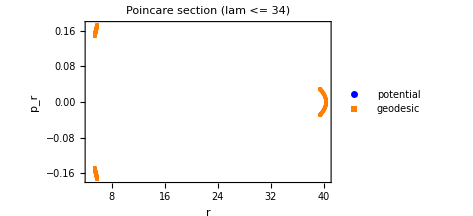

```mathematica
ListPlot[{cross[[All,{2,3}]],refP[[All,{2,3}]]},PlotStyle->{Blue,Orange},PlotMarkers->{Automatic,3},PlotRange->All,Frame->True,Axes->False,ImageSize->350,PlotLabel->"Poincare section (lam <= 34)",FrameLabel->{"r","p_r"},PlotLegends->{"potential","geodesic"}]
```

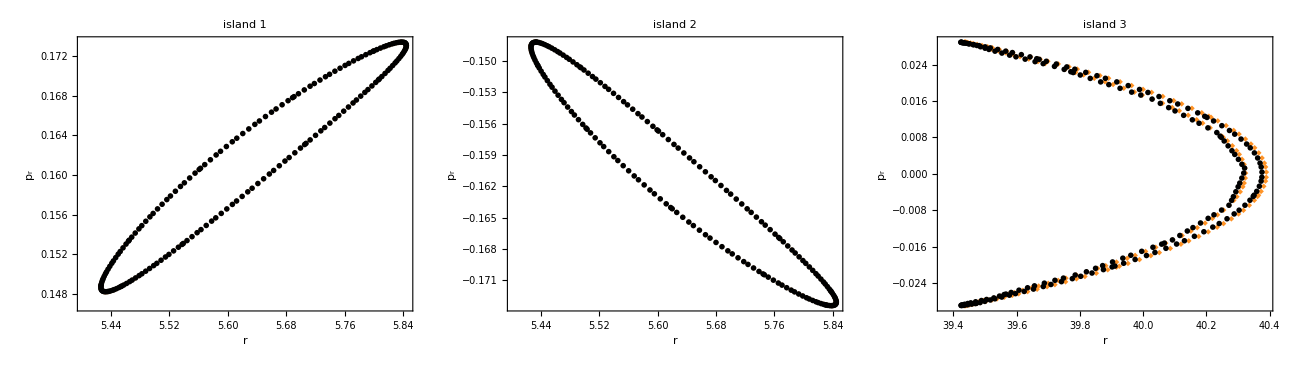

```mathematica
isl[d_,o_]:=d[[o;; ;;3,{2,3}]];

refCol=Lighter[Orange,0.15];
refMark=Graphics[{refCol,Polygon[{{0,1},{1,0},{0,-1},{-1,0}}]}];
runMark=Graphics[{Black,Disk[]}];

pan[o_]:=ListPlot[{isl[refP,o],isl[cross,o]},(*reference first=underneath*)PlotMarkers->{{refMark,0.035},{runMark,0.01}},PlotRange->All,PlotRangePadding->Scaled[0.05],Frame->True,Axes->False,ImageSize->430,AspectRatio->0.8,PlotLabel->"island "<>ToString[o],FrameLabel->{"r",Subscript["p","r"]},ImagePadding->{{58,12},{45,22}}];

islandFig=Legended[GraphicsRow[{pan[1],pan[2],pan[3]},Spacings->0,ImageSize->1290],Placed[PointLegend[{refCol,Black},{"reference","this run"},LegendMarkers->{refMark,runMark},LegendMarkerSize->10,LegendLayout->"Row"],Below]];

islandFig
```

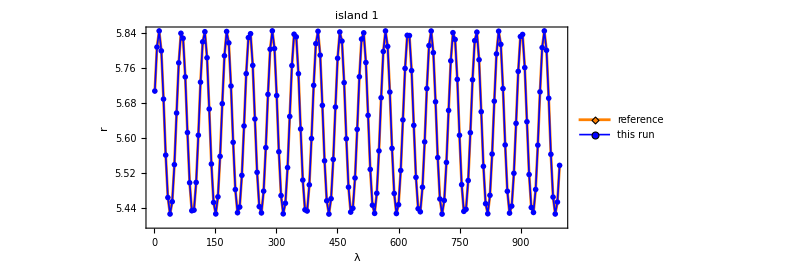
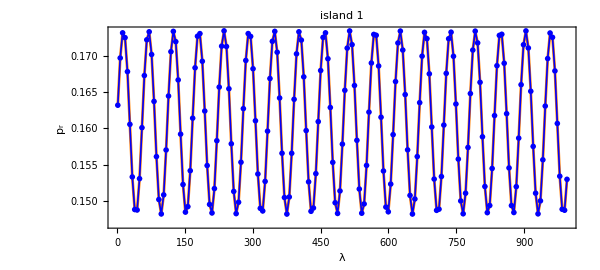
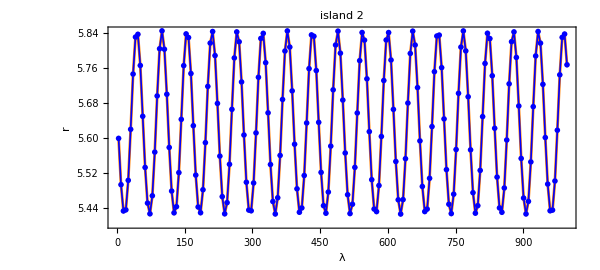
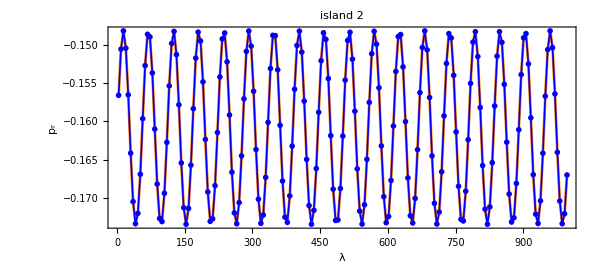
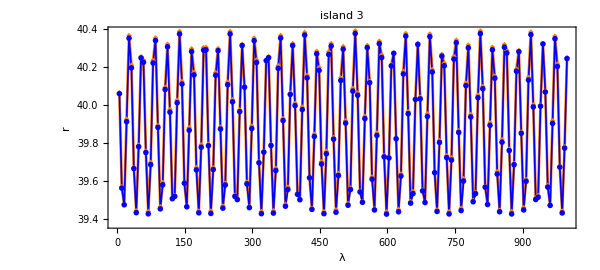
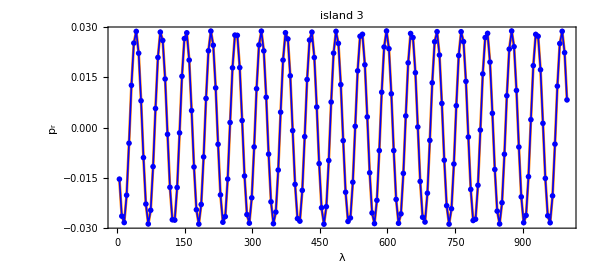
r  vs  λ | p_r  vs  λ
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
ts[d_,o_,c_]:=d[[o;; ;;3,{1,c}]];   (*c=2 for r,3 for p_r*)

refCol=Orange;
runCol=Blue;
refMark=Graphics[{refCol,Polygon[{{0,1},{1,0},{0,-1},{-1,0}}]}];
runMark=Graphics[{runCol,Disk[]}];
refLine=Directive[refCol,AbsoluteThickness[2]];
runLine=Directive[runCol,AbsoluteThickness[1.2]];

tsPan[o_,c_,ylbl_]:=ListLinePlot[{ts[refP,o,c],ts[cross,o,c]},(*reference first=underneath*)PlotStyle->{refLine,runLine},PlotMarkers->{{refMark,0.035},{runMark,0.018}},PlotRange->All,PlotRangePadding->Scaled[0.05],Frame->True,Axes->False,ImageSize->600,AspectRatio->0.45,PlotLabel->"island "<>ToString[o],FrameLabel->{"λ",ylbl},ImagePadding->{{62,12},{45,22}}];

tsLegend=Placed[LineLegend[{refLine,runLine},{"reference","this run"},LegendMarkers->{refMark,runMark},LegendMarkerSize->14,LegendLayout->"Row"],Below];

colHead[txt_]:=Style[txt,FontFamily->"Times",FontSize->18,Bold];

islandTS=Legended[Grid[Prepend[Table[{tsPan[o,2,"r"],tsPan[o,3,Subscript["p","r"]]},{o,3}],{colHead[Row[{"r  vs  ","λ"}]],colHead[Row[{Subscript["p","r"],"  vs  ","λ"}]]}],Spacings->{0,{1,0.5,0,0}},Alignment->Center],tsLegend];

islandTS

Export[FileNameJoin[{NotebookDirectory[],"islands_vs_lambda.pdf"}],islandTS];
Export[FileNameJoin[{NotebookDirectory[],"islands_vs_lambda.png"}],islandTS,ImageResolution->300];
```

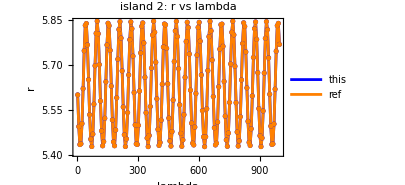

```mathematica
ListLinePlot[{tsl[cross,2],tsl[refP,2]},PlotStyle->{Blue,Orange},Mesh->All,MeshStyle->PointSize[0.012],PlotRange->All,Frame->True,Axes->False,ImageSize->300,PlotLabel->"island 2: r vs lambda",FrameLabel->{"lambda","r"},PlotLegends->{"integrated","ref"}]
```

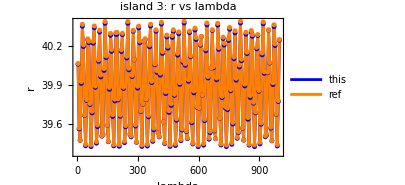

```mathematica
ListLinePlot[{tsl[cross,3],tsl[refP,3]},PlotStyle->{Blue,Orange},Mesh->All,MeshStyle->PointSize[0.012],PlotRange->All,Frame->True,Axes->False,ImageSize->300,PlotLabel->"island 3: r vs lambda",FrameLabel->{"lambda","r"},PlotLegends->{"integrated","ref"}]
```

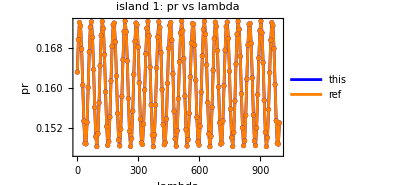

```mathematica
ListLinePlot[{tsp[cross,1],tsp[refP,1]},PlotStyle->{Blue,Orange},Mesh->All,MeshStyle->PointSize[0.012],PlotRange->All,Frame->True,Axes->False,ImageSize->300,PlotLabel->"island 1: pr vs lambda",FrameLabel->{"lambda","pr"},PlotLegends->{"integrated","ref"}]
```

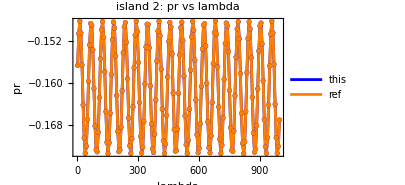

```mathematica
ListLinePlot[{tsp[cross,2],tsp[refP,2]},PlotStyle->{Blue,Orange},Mesh->All,MeshStyle->PointSize[0.012],PlotRange->All,Frame->True,Axes->False,ImageSize->300,PlotLabel->"island 2: pr vs lambda",FrameLabel->{"lambda","pr"},PlotLegends->{"integrated","ref"}]
```

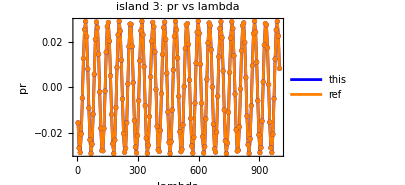

```mathematica
ListLinePlot[{tsp[cross,3],tsp[refP,3]},PlotStyle->{Blue,Orange},Mesh->All,MeshStyle->PointSize[0.012],PlotRange->All,Frame->True,Axes->False,ImageSize->300,PlotLabel->"island 3: pr vs lambda",FrameLabel->{"lambda","pr"},PlotLegends->{"integrated","ref"}]
```

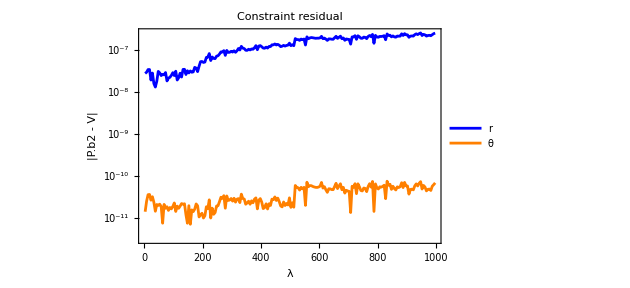
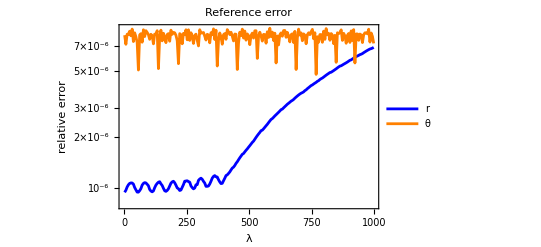
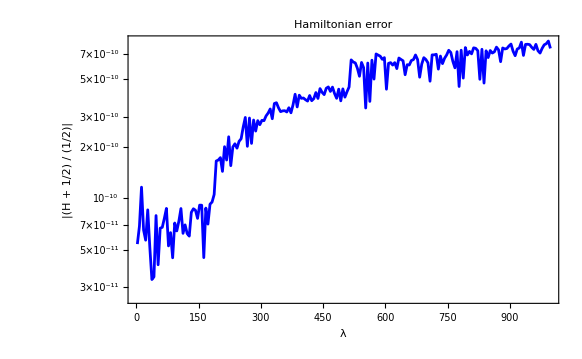

```mathematica
(* ===================================================================ENVELOPE PLOTS Max|error|in windows of width wEnv (5 lambda, ~2 radial periods).
===================================================================*)wEnv=5.;
envMax[data_,w_]:={Mean[#[[All,1]]],Max[#[[All,2]]]}&/@GatherBy[data,Floor[#[[1]]/w]&];

Column[{ListLogPlot[{envMax[res1,wEnv],envMax[res2,wEnv]},Joined->True,PlotStyle->{Blue,Orange},PlotRange->All,Frame->True,Axes->False,ImageSize->400,PlotLabel->"Constraint residual",FrameLabel->{"λ","|P.b2 - V|"},PlotLegends->{"r","θ"}],ListLogPlot[{envMax[errR,wEnv],envMax[errTh,wEnv]},Joined->True,PlotStyle->{Blue,Orange},PlotRange->All,Frame->True,Axes->False,ImageSize->400,PlotLabel->"Reference error",FrameLabel->{"λ","relative error"},PlotLegends->{"r","θ"}],ListLogPlot[envMax[hErr,wEnv],Joined->True,PlotStyle->Blue,PlotRange->All,Frame->True,Axes->False,ImageSize->400,PlotLabel->"Hamiltonian error",FrameLabel->{"λ","|(H + 1/2) / (1/2)|"}]}]
```

matched 561 of 561 crossings   (ref has 561)

island label mismatches: 0

island | n | med |dr| | max |dr| | med |dpr| | max |dpr|
1 | 187 | 0.000178923 | 0.000264134 | 0.0000110773 | 0.0000140596
2 | 187 | 0.000135316 | 0.000268806 | 8.28619×10^-6 | 0.0000147477
3 | 187 | 0.0113683 | 0.0147044 | 0.0000190973 | 0.0000447714

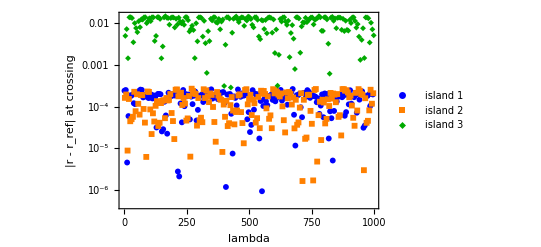
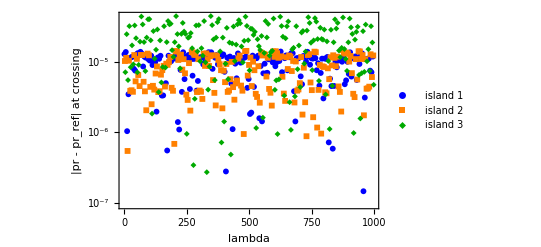

matched 561 of 561 crossings   (ref has 561)

island label mismatches: 0

island | n | med |dr| | max |dr| | med |dpr| | max |dpr|
1 | 187 | 0.000178923 | 0.000264134 | 0.0000110773 | 0.0000140596
2 | 187 | 0.000135316 | 0.000268806 | 8.28619×10^-6 | 0.0000147477
3 | 187 | 0.0113683 | 0.0147044 | 0.0000190973 | 0.0000447714

-Graphics-
-Graphics-

```mathematica
(* ===================================================================POINCARE CROSSING ERRORS BY ISLAND Pairs each crossing in cross with the nearest-in-lambda crossing in refP and plots|dr|and|dpr|per crossing,one colour per island.Island of crossing k=Mod[k-1,3]+1,the same convention as isl/tsl/tsp.Pairs further apart than a quarter of the typical crossing spacing are dropped (e.g.past the end of the reference file).islandOK flags pairs whose island labels disagree,which would mean one run gained or lost a crossing and the comparison has shifted by one.Run after the crossing cell (needs cross,refP).
===================================================================*)crossErr=Module[{nf,sp,tol},nf=Nearest[refP[[All,1]]->Range[Length[refP]]];
sp=Median[Differences[cross[[All,1]]]];
tol=0.25 sp;
Table[With[{j=First[nf[cross[[k,1]]]]},If[Abs[cross[[k,1]]-refP[[j,1]]]<tol,{cross[[k,1]],Mod[k-1,3]+1,Abs[cross[[k,2]]-refP[[j,2]]]+10^-18,Abs[cross[[k,3]]-refP[[j,3]]]+10^-18,Mod[k-j,3]==0},Nothing]],{k,Length[cross]}]];

Print["matched ",Length[crossErr]," of ",Length[cross]," crossings   (ref has ",Length[refP],")"];
Print["island label mismatches: ",Count[crossErr[[All,5]],False]];
Print[TableForm[Table[With[{s=Select[crossErr,#[[2]]==o&]},{o,Length[s],Median[s[[All,3]]],Max[s[[All,3]]],Median[s[[All,4]]],Max[s[[All,4]]]}],{o,3}],TableHeadings->{None,{"island","n","med |dr|","max |dr|","med |dpr|","max |dpr|"}}]];

islErrPlot[col_,lbl_]:=ListLogPlot[Table[Select[crossErr,#[[2]]==o&][[All,{1,col}]],{o,3}],PlotStyle->{Blue,Orange,Darker[Green]},PlotMarkers->{Automatic,6},PlotRange->All,Frame->True,Axes->False,ImageSize->400,FrameLabel->{"lambda",lbl},PlotLegends->{"island 1","island 2","island 3"}];

plot=Column[{islErrPlot[3,"|r - r_ref| at crossing"],islErrPlot[4,"|pr - pr_ref| at crossing"]}]
Export[FileNameJoin[{NotebookDirectory[],"poincare_error.pdf"}],plot];
Export[FileNameJoin[{NotebookDirectory[],"poincare_error.png"}],plot,ImageResolution->300];
```